```mathematica
L1 = {116.60, 116.50, 116.50};
L2 = {7.40, 7.45, 7.45};
Ug = {0.018, 0.520, 1.01, 2.00, 3.05, 3.63, 4.61};
l1 = Mean[L1];
l2 = Mean[L2];
L = l1 - l2;
mass = {0, 100, 200, 300, 400, 500, 600};
lo= 12.564;
l = {12.564, 12.742, 12.945, 13.138, 13.342, 13.541, 13.800};
deltaL =(l - lo) ;
actualDeltaL = deltaL* (L/l1)
```

{0.,0.166646,0.356697,0.537386,0.728374,0.91468,1.15716}

```mathematica
fitDataA = Transpose[{mass, actualDeltaL}];
fitA = LinearModelFit[fitDataA, x, x]
%["ParameterTable"]
line = Fit[fitDataA, {1, x}, x]
Show[ListPlot[fitDataA, PlotStyle->Black, PlotMarkers->{Style["X",10]}],
Plot[line, {x, 0, 650}, PlotStyle->Gray],
AxesLabel->{Style["质量(g)",15,Bold], Style["ΔL(mm)", 15, Bold]},
PlotLabel->Style["砝码质量与金属丝伸长量关系的拟合曲线",18,FontFamily->"Hack Nerd Font", Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]
```

FittedModel[-0.0204964+0.00190686 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0204964 | 0.0146193 | -1.40201 | 0.219839
x | 0.00190686 | 0.0000405466 | 47.0289 | 8.21065×10^-8

-0.0204964+0.00190686 x

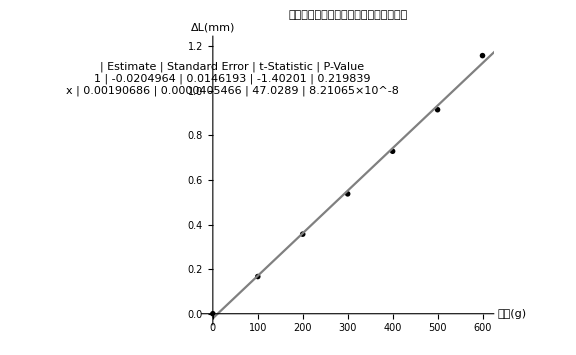

```mathematica
fitDataB = Transpose[{actualDeltaL, Ug}];
fitB = LinearModelFit[fitDataB,x,x]
%["ParameterTable"]
lineB = Fit[fitDataB, {1,x},x]
Show[ListPlot[fitDataB,PlotStyle->Black,PlotMarkers->{Style["X",10]}],
Plot[lineB, {x,0,1.2},PlotStyle->Gray],
AxesLabel->{Style["金属丝实际伸长长度(mm)",15,Bold],Style["Ug(mV)",15,Bold]},
PlotLabel->Style["Ug与金属丝实际伸长长度拟合曲线",18,FontFamily->"Hack Nerd Font",Bold],
ImageSize->Large]
```

FittedModel[-0.158024+4.12961 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.158024 | 0.121773 | -1.29769 | 0.251033
x | 4.12961 | 0.18153 | 22.7489 | 3.05177×10^-6

-0.158024+4.12961 x